```mathematica
LinguisticAssistant
```

```mathematica
Formula1 = (x - 2 )/(x^2 - x + 4);
Formula2 = D[Formula1, x]
```

-((-2+x) (-1+2 x))/((4-x+x^2)^2)+1/(4-x+x^2)

```mathematica
Simplify[Formula2]
```

```mathematica
(2+4 x-x^2)/((4-x+x^2)^2)
D[Formula1, x] /. x-> Sqrt[2.]
Formula2 /. x -> Sqrt[2.]
```

(2+4 x-x^2)/((4-x+x^2)^2)

0.268997

```mathematica
0.2689969389971543
Formula3 = Simplify[D[Formula1, {x, 3}]]
Formula3 /. x -> Sqrt[1.π]
```

0.268997

-(6 (-2+40 x-12 x^2-8 x^3+x^4))/((4-x+x^2)^4)

```mathematica
0.025110738055369907
Formula4 = 1/(ax^2 + bxy + cy^2)
Formula5 = Simplify[D[Formula4, {x, 3}]]
```

0.0251107

1/(ax^2+bxy+cy^2)

0

```mathematica
FunctionOne[x_] := (x - 2)/(x^2-x+4)
```

```mathematica
Function[x,(x-2)/(x^2-x+4)]
```

Function[x,(x-2)/(x^2-x+4)]

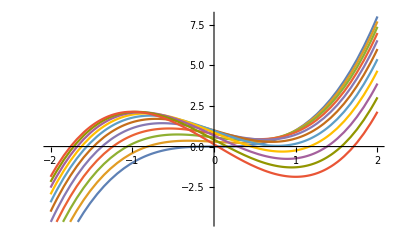

```mathematica
Clear[f];
f[c_][x_] := x^3 - c x + Sin[c];
{ca, cb, nn} = {0, 3, 10};
Listf := Table[ f[c][x], {c, ca, cb, (cb - ca) / nn}];
Plot[Listf, {x, -2, 2}]
```

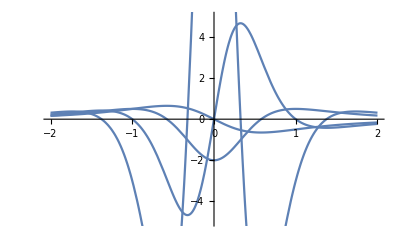

```mathematica
f[x_] := 1/(x^2 + 1);
fhigher[k_] := Derivative[k][f];
HigherDer = Table[Plot[ fhigher[k][z], {z, -2, 2}], {k, 1, 4}];
Show[HigherDer, PlotRange-> {-5, 5}]
```

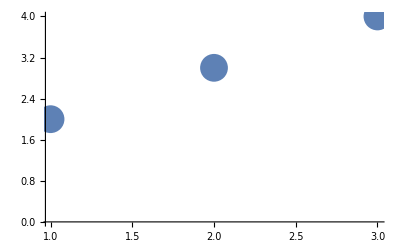

```mathematica
P1 = {1, 2}; P2 = {3, 4}; P3 = {2, 3};
ListPlot[ {P1, P2, P3}, PlotStyle -> PointSize[.05]]
```

{{0.841471,1.55741},{0.909297,1.15782},{0.14112,-0.452316},{-0.756802,0.300632},{-0.958924,-0.133526},{-0.279415,7.75047},{0.656987,-3.17291},{0.989358,2.34786},{0.412118,-0.810994},{-0.544021,-0.587214},{-0.99999,-20.5249},{-0.536573,-0.563649},{0.420167,-0.753917},{0.990607,2.74342},{0.650288,-2.53211},{-0.287903,25.1116},{-0.961397,-0.0265304},{-0.750987,0.441732},{0.149877,-0.290973},{0.912945,1.61988},{0.836656,2.40693},{-0.00885131,0.197231},{-0.84622,2.66998},{-0.905578,1.91031},{-0.132352,-0.178808},{0.762558,0.623583},{0.956376,0.151651},{0.270906,-5.73498},{-0.663634,-1.38906},{-0.988032,15.0619}}

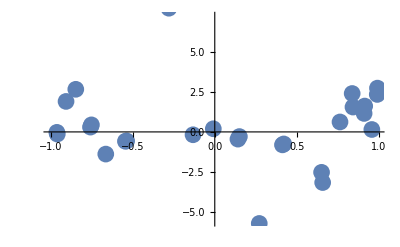

```mathematica
PointList = Table[ {1. Sin[k], 1.Tan[k^2]}, {k, 1, 30}]
ListPlot[ PointList, PlotStyle -> PointSize[.03]]
```

```mathematica
Figure[c_] := Plot[Sin[c x]^3 - Sin[c^3 + x] + 1,
{x, -2, 2}];
{a, b} = {1, 3};
Manipulate[
Show[Figure[c], PlotRange -> {{-a, a}, {-b, b}}],
{c, -5, 5, .01}]
```

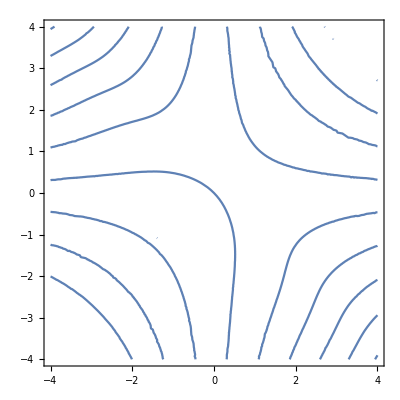

```mathematica
a = 4;
ContourPlot[Tan[x y] - (x + y) == 0, {x, -a, a}, {y, -a, a}]
```

```mathematica
LinguisticAssistant
```

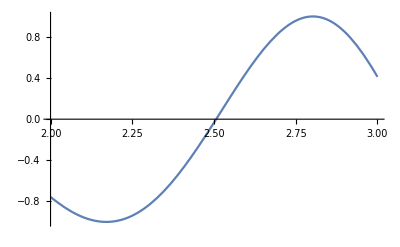

5 Cos[25/4]

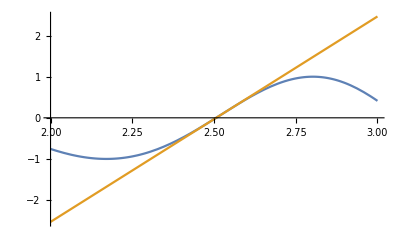

```mathematica
f[x_] := Sin[x^2];
a = 2; b = 3;
Plot[ f[x], {x, a, b}]
c = (a + b) / 2;
f'[c]
m = f'[c];
TL[x_] := f[c] + m(x - c);
Plot[ {f[x], TL[x]}, {x, a, b}]
```